```mathematica
Quit[];
```

```mathematica
"先取出车板极端加速度数据"
```

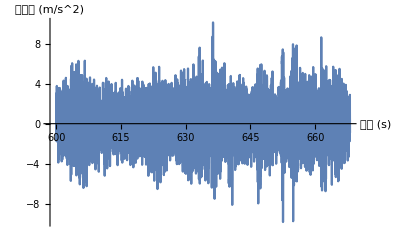

```mathematica
(*1. 定义路径和 Sheet 名*)filePath="C:\Users\ych\Documents\时域1.xlsx";
sheetName="XTCZJ4_Waveform(3)";(*请确保这个名字和 Excel 底部标签完全一致*)(*2. 先完整导入指定的 Sheet（13000多行，对MMA来说瞬间完成）*)allData=Import[filePath,{"Sheets",sheetName}];

(*3. 在内存中精准截取：[[2;;13260,{3,7}]] 的含义是——取第 2 行到第 13260 行，只取第 3 列（C列）和第 7 列（G列）*)
data=allData[[2;;13620,{3,7}]];

(*4. 拆分时间与加速度*)
time=data[[All,1]];
accel=data[[All,2]];

(*5. 绘图验证*)
ListPlot[data,Joined->True,AxesLabel->{"时间 (s)","加速度 (m/s^2)"},PlotRange->All]
```

```mathematica
"将点列转化为函数"
```

```mathematica
accelFunc=Interpolation[data];
```

```mathematica
"对比图形"
```

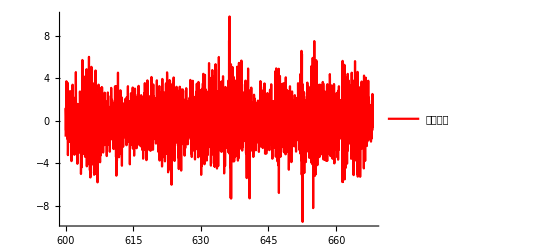

```mathematica
Plot[accelFunc[t],{t,time[[1]],time[[-1]]},PlotStyle->{Red,Thick},PlotLegends->{"插值曲线"},PlotRange->All]
```

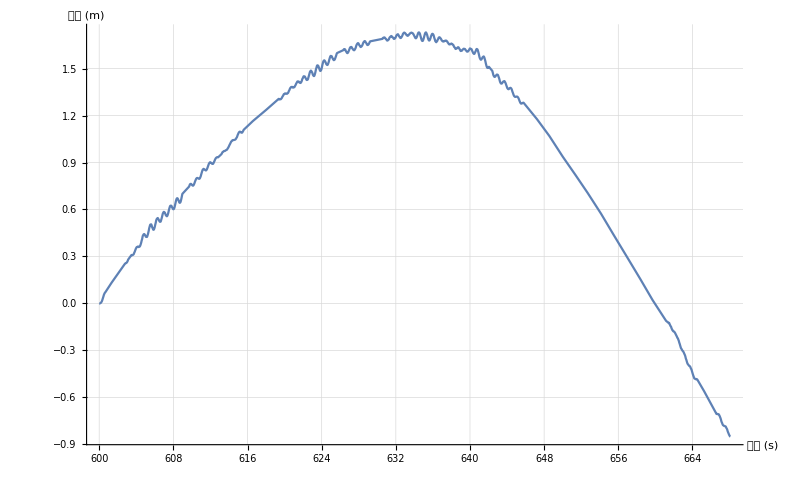

```mathematica
(*1. 定义初始时刻和结束时刻*)t0=600;
tEnd=time[[-1]];(*数据最后一行的时间*)(*2. 用 NDSolve 求解速度和位移*)sol=NDSolve[{v'[t]==accelFunc[t],(*加速度是速度的导数*)x'[t]==v[t],(*速度是位移的导数*)v[t0]==0,(*初始速度条件*)x[t0]==0              (*初始位移条件*)},{x,v},{t,t0,tEnd}];

(*3. 提取位移函数 x(t)*)
xFunc=x/.sol[[1]];

(*4. 画出位移曲线*)
Plot[xFunc[t],{t,t0,tEnd},AxesLabel->{"时间 (s)","位移 (m)"},PlotRange->All,GridLines->Automatic]
```

```mathematica
x0[t_]=-xFunc[t];
```

```mathematica
"参数取值"
```

```mathematica
d=0.2;l1=0.0125;l2=0.02;m1=1647;m2=20000;k1=499200000;k2=581304600;
```

```mathematica
"定义弹簧分段函数"
```

```mathematica
dx1[t_]=Piecewise[{{l1-(x1[t]-x0[t]),l1-(x1[t]-x0[t])>0}},0];dx2[t_]=Piecewise[{{l2-(x2[t]-x1[t]-d),l2-(x2[t]-x1[t]-d)>0}},0];
```

```mathematica
(*直接改写*)dx1[t_]=(l1-(x1[t]-x0[t]))*UnitStep[l1-(x1[t]-x0[t])];
dx2[t_]=(l2-(x2[t]-x1[t]-d))*UnitStep[l2-(x2[t]-x1[t]-d)];
```

```mathematica
"解ODE"
```

```mathematica
qqss=NDSolve[{-m2*9.8+k2*dx2[t]==m2*x2''[t],-m1*9.8-k2*dx2[t]+k1*dx1[t]==m1*x1''[t],x1[601]==0.012075,x1'[601]==0,x2[601]==0.231738,x2'[601]==0},{x1,x2},{t,601,661},MaxSteps->10^10];
```

```mathematica
qqx1=First[x1/.qqss];qqx2=First[x2/.qqss];
```

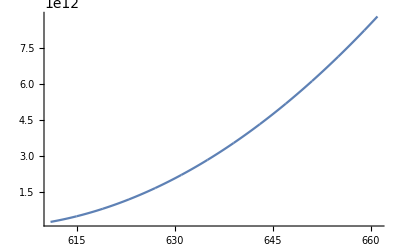

```mathematica
Plot[-m1*9.8-k2*dx2[t]+k1*dx1[t]/.qqss,{t,611,661},PlotPoints->100000,PlotRange->All]
```

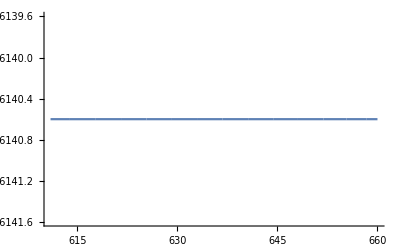

```mathematica
Plot[m1*x1''[t]/.qqss,{t,611,660},PlotPoints->100000,PlotRange->All]
```

```mathematica
(*直接改写*)dx1[t_]=(l1-(x1[t]-x0[t]))*UnitStep[l1-(x1[t]-x0[t])];
dx2[t_]=(l2-(x2[t]-x1[t]-d))*UnitStep[l2-(x2[t]-x1[t]-d)];
```

```mathematica
dx1[611]/.qqss
```

{491.102}

```mathematica
l1-(x1[611]-x0[611])/.qqss
```

{491.102}

```mathematica
x0[601]
```

-0.0920713

```mathematica
dx1[t_]=l1-(x1[t]-x0[t]);dx2[t_]=l2-(x2[t]-x1[t]-d);
```